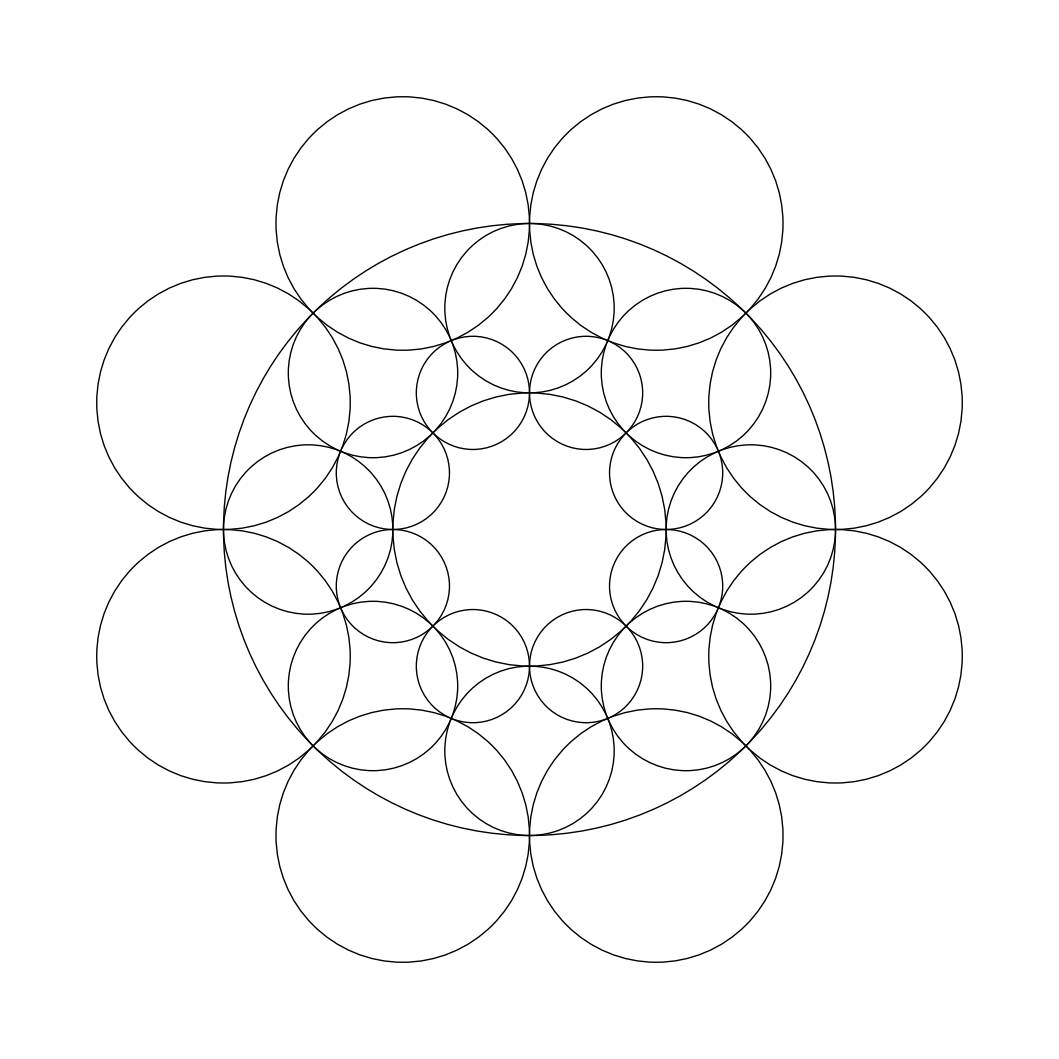

```mathematica
n=8;
gram=IdentityMatrix[3n+2]//MatrixForm;
regularcoords=ConstantArray[0,{3,3n+2}]//MatrixForm;
(*Order is X, Y, R
unit circle passes through the centers of circles 1-n
1-n ring
n+1 inner 
n+2 outer
n+3-2n+2 inner dualS
2n+3-3n+2 outer dual*)
For[i=0,i<n,i++,regularcoords[[1,1,i+1]]=Cos[2Pi*i/n];regularcoords[[1,2,i+1]]=Sin[2Pi*i/n];regularcoords[[1,3,i+1]]=Sin[Pi/n]];
regularcoords[[1,3,n+1]]=1-Sin[Pi/n];
regularcoords[[1,3,n+2]]=-1-Sin[Pi/n];
For[i=0,i<n,i++,regularcoords[[1,1,i+n+3]]=(Sec[Pi/n]-Tan[Pi/n])Cos[(2 i+1)Pi/n];regularcoords[[1,2,i+n+3]]=(Sec[Pi/n]-Tan[Pi/n])Sin[(2 i+1)Pi/n];regularcoords[[1,3,i+n+3]]=(Sec[Pi/n]-Tan[Pi/n])Sin[Pi/n]];
For[i=0,i<n,i++,regularcoords[[1,1,i+2n+3]]=(Sec[Pi/n]+Tan[Pi/n])Cos[(2 i+1)Pi/n];regularcoords[[1,2,i+2n+3]]=(Sec[Pi/n]+Tan[Pi/n])Sin[(2 i+1)Pi/n];regularcoords[[1,3,i+2n+3]]=(Sec[Pi/n]+Tan[Pi/n])Sin[Pi/n]];
Graphics[{Table[Circle[{regularcoords[[1,1,i]],regularcoords[[1,2,i]]},Abs[regularcoords[[1,3,i]]]],{i,Length[regularcoords[[1,1]]]}]}]
```

```mathematica
xyrtoabbc[{x_,y_,r_}]:={r(x^2/r^2+y^2/r^2-1),1/r,x/r,y/r}
```

```mathematica
abbctoxyr[{bt_,b_,h1_,h2_}]:={h1/b,h2/b,1/b}
```

```mathematica
graphCircles[circs_]:=Graphics[Circle[{#⟦1⟧,#⟦2⟧},Abs[#⟦3⟧]]&/@circs]
```

```mathematica
graphAbbc[circs_]:=graphCircles[abbctoxyr/@circs]
```

```mathematica
findRoot[tuple_,sigmas_]:=Block[{candidates},
candidates=Select[sigmas,Total[#.tuple]<Total[tuple]&];
If[Length[candidates]==0,tuple,findRoot[candidates⟦1⟧.tuple,sigmas]]]
```

```mathematica
MatrixForm[mycoords=(xyrtoabbc/@(Transpose[regularcoords⟦1⟧])//Simplify)⟦n+3;;3n+2⟧];
```

```mathematica
W=mycoords//N;
```

```mathematica
scale[a_]:={{a, 0, 0, 0}, {0, 1/a, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}
```

```mathematica
rotate[θ_]:={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[θ], Sin[θ]}, {0, 0, -Sin[θ], Cos[θ]}}
```

```mathematica
translate[s_,t_]:={{1, s^2+t^2, 2s, 2t}, {0, 1, 0, 0}, {0, s, 1, 0}, {0, t, 0, 1}}
```

```mathematica
invert:={{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}
```

```mathematica
invertAboutCircle[x_,y_,r_]:=translate[x,y].scale[r].invert.scale[1/r].translate[-x,-y]
```

```mathematica
W2=invertAboutCircle[regularcoords⟦1⟧⟦1⟧⟦-1⟧,regularcoords⟦1⟧⟦2⟧⟦-1⟧,regularcoords⟦1⟧⟦3⟧⟦-1⟧].#&/@W//Chop;
```

```mathematica
W2//MatrixForm
```

(21.5189 | 14.387 | 16.8995 | -5.
53.7544 | 31.2482 | 38.799 | -13.2426
85.9898 | 48.1094 | 60.1127 | -22.8995
99.3422 | 55.0936 | 68.3553 | -28.3137
85.9898 | 48.1094 | 58.6985 | -26.3137
53.7544 | 31.2482 | 36.799 | -18.0711
21.5189 | 14.387 | 15.4853 | -8.41421
8.16652 | 7.40289 | 7.24264 | -3.
10.0143 | 5.2381 | 7.24264 | -1.
42.2498 | 22.0993 | 29.1421 | -9.24264
74.4852 | 38.9605 | 50.4558 | -18.8995
87.8376 | 45.9447 | 58.6985 | -24.3137
74.4852 | 38.9605 | 49.0416 | -22.3137
42.2498 | 22.0993 | 27.1421 | -14.0711
10.0143 | 5.2381 | 5.82843 | -4.41421
-3.33809 | -1.74603 | -2.41421 | 1.)

```mathematica
W2⟦All,2⟧
```

{14.387,31.2482,48.1094,55.0936,48.1094,31.2482,14.387,7.40289,5.2381,22.0993,38.9605,45.9447,38.9605,22.0993,5.2381,-1.74603}

```mathematica
sigmas=findGeneratorsFromG[Simplify[prismG[n]]]//Chop
```

{{{1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1.,0,0,0,0,0,0,0,-1.,1.,0,0,0,0,0,0},{4.41421,0,0,0,0,0,0,0,-2.41421,6.82843,-1.,0,0,0,0,0},{9.24264,0,0,0,0,0,0,0,-3.41421,14.0711,-2.41421,0,0,0,0,0},{12.6569,0,0,0,0,0,0,0,-3.41421,18.4853,-3.41421,0,0,0,0,0},{12.6569,0,0,0,0,0,0,0,-2.41421,17.4853,-3.41421,0,0,0,0,0},{9.24264,0,0,0,0,0,0,0,-1.,11.6569,-2.41421,0,0,0,0,0},{4.41421,0,0,0,0,0,0,0,0,4.41421,-1.,0,0,0,0,0},{0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0},{3.41421,0,0,0,0,0,0,0,-1.41421,6.82843,-1.,0,0,0,0,0},{8.24264,0,0,0,0,0,0,0,-2.41421,14.0711,-2.41421,0,0,0,0,0},{11.6569,0,0,0,0,0,0,0,-2.41421,18.4853,-3.41421,0,0,0,0,0},{11.6569,0,0,0,0,0,0,0,-1.41421,17.4853,-3.41421,0,0,0,0,0},{8.24264,0,0,0,0,0,0,0,0,11.6569,-2.41421,0,0,0,0,0},{3.41421,0,0,0,0,0,0,0,1.,4.41421,-1.,0,0,0,0,0}},{{0,1.20711,0,-0.707107,0,0.5,0,0,0,0,0,0,0,0,0,0},{0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.5,0,0.707107,0,-0.207107,0,0,0,0,0,0,0,0,0,0},{0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0},{0,-0.207107,0,0.707107,0,0.5,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0},{0,0.5,0,-0.707107,0,1.20711,0,0,0,0,0,0,0,0,0,0},{0,1.,0,-1.,0,1.,0,0,0,0,0,0,0,0,0,0},{0,1.55025,0,-0.707107,0,1.84315,0,0,0,0,0,0,0,-1.,0,0},{0,1.34315,0,0,0,1.34315,0,0,0,0,0,0,0,-1.,0,0},{0,0.843146,0,0.707107,0,1.13604,0,0,0,0,0,0,0,-1.,0,0},{0,0.343146,0,1.,0,1.34315,0,0,0,0,0,0,0,-1.,0,0},{0,0.136039,0,0.707107,0,1.84315,0,0,0,0,0,0,0,-1.,0,0},{0,0.343146,0,0,0,2.34315,0,0,0,0,0,0,0,-1.,0,0},{0,0.843146,0,-0.707107,0,2.55025,0,0,0,0,0,0,0,-1.,0,0},{0,1.34315,0,-1.,0,2.34315,0,0,0,0,0,0,0,-1.,0,0}},{{0,0,0,0,0,0,0,1.,1.,0,0,0,0,0,0,-1.},{0,0,0,0,0,0,-1.,5.41421,4.41421,0,0,0,0,0,0,-1.},{0,0,0,0,0,0,-2.41421,11.6569,8.24264,0,0,0,0,0,0,0},{0,0,0,0,0,0,-3.41421,16.0711,10.2426,0,0,0,0,0,0,1.41421},{0,0,0,0,0,0,-3.41421,16.0711,9.24264,0,0,0,0,0,0,2.41421},{0,0,0,0,0,0,-2.41421,11.6569,5.82843,0,0,0,0,0,0,2.41421},{0,0,0,0,0,0,-1.,5.41421,2.,0,0,0,0,0,0,1.41421},{0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1.,4.41421,4.41421,0,0,0,0,0,0,0},{0,0,0,0,0,0,-2.41421,10.6569,8.24264,0,0,0,0,0,0,1.},{0,0,0,0,0,0,-3.41421,15.0711,10.2426,0,0,0,0,0,0,2.41421},{0,0,0,0,0,0,-3.41421,15.0711,9.24264,0,0,0,0,0,0,3.41421},{0,0,0,0,0,0,-2.41421,10.6569,5.82843,0,0,0,0,0,0,3.41421},{0,0,0,0,0,0,-1.,4.41421,2.,0,0,0,0,0,0,2.41421},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.}},{{0,4.41421,0,0,0,0,0,0,0,0.414214,3.41421,0,-0.414214,0,0,0},{0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1.,0,0,0,0,0,0,0,-1.,1.,0,0,0,0,0},{0,4.41421,0,0,0,0,0,0,0,-2.,5.82843,0,-0.414214,0,0,0},{0,9.24264,0,0,0,0,0,0,0,-2.41421,11.6569,0,-1.,0,0,0},{0,12.6569,0,0,0,0,0,0,0,-2.,15.0711,0,-1.41421,0,0,0},{0,12.6569,0,0,0,0,0,0,0,-1.,14.0711,0,-1.41421,0,0,0},{0,9.24264,0,0,0,0,0,0,0,0,9.24264,0,-1.,0,0,0},{0,3.41421,0,0,0,0,0,0,0,1.41421,3.41421,0,-0.414214,0,0,0},{0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0},{0,3.41421,0,0,0,0,0,0,0,-1.,5.82843,0,-0.414214,0,0,0},{0,8.24264,0,0,0,0,0,0,0,-1.41421,11.6569,0,-1.,0,0,0},{0,11.6569,0,0,0,0,0,0,0,-1.,15.0711,0,-1.41421,0,0,0},{0,11.6569,0,0,0,0,0,0,0,0,14.0711,0,-1.41421,0,0,0},{0,8.24264,0,0,0,0,0,0,0,1.,9.24264,0,-1.,0,0,0}},{{0,-2.41421,14.0711,-2.41421,0,0,0,0,0,0,0,8.24264,0,0,0,0},{0,-1.,6.82843,-1.41421,0,0,0,0,0,0,0,3.41421,0,0,0,0},{0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1.,4.41421,1.,0,0,0,0,0,0,0,3.41421,0,0,0,0},{0,-2.41421,11.6569,0,0,0,0,0,0,0,0,8.24264,0,0,0,0},{0,-3.41421,17.4853,-1.41421,0,0,0,0,0,0,0,11.6569,0,0,0,0},{0,-3.41421,18.4853,-2.41421,0,0,0,0,0,0,0,11.6569,0,0,0,0},{0,-2.41421,14.0711,-3.41421,0,0,0,0,0,0,0,9.24264,0,0,0,0},{0,-1.,6.82843,-2.41421,0,0,0,0,0,0,0,4.41421,0,0,0,0},{0,0,1.,-1.,0,0,0,0,0,0,0,1.,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0},{0,-1.,4.41421,0,0,0,0,0,0,0,0,4.41421,0,0,0,0},{0,-2.41421,11.6569,-1.,0,0,0,0,0,0,0,9.24264,0,0,0,0},{0,-3.41421,17.4853,-2.41421,0,0,0,0,0,0,0,12.6569,0,0,0,0},{0,-3.41421,18.4853,-3.41421,0,0,0,0,0,0,0,12.6569,0,0,0,0}},{{0,0,0,2.,10.6569,0,0,0,0,-1.41421,0,13.0711,0,0,0,0},{0,0,0,2.41421,6.82843,0,0,0,0,-1.,0,9.24264,0,0,0,0},{0,0,0,2.,2.41421,0,0,0,0,-0.414214,0,3.82843,0,0,0,0},{0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-0.414214,4.82843,0,0,0,0,-0.414214,0,3.82843,0,0,0,0},{0,0,0,0,9.24264,0,0,0,0,-1.,0,9.24264,0,0,0,0},{0,0,0,1.,11.6569,0,0,0,0,-1.41421,0,13.0711,0,0,0,0},{0,0,0,1.,10.6569,0,0,0,0,-1.41421,0,14.0711,0,0,0,0},{0,0,0,1.41421,6.82843,0,0,0,0,-1.,0,10.2426,0,0,0,0},{0,0,0,1.,2.41421,0,0,0,0,-0.414214,0,4.82843,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0},{0,0,0,-1.,1.,0,0,0,0,0,0,1.,0,0,0,0},{0,0,0,-1.41421,4.82843,0,0,0,0,-0.414214,0,4.82843,0,0,0,0},{0,0,0,-1.,9.24264,0,0,0,0,-1.,0,10.2426,0,0,0,0},{0,0,0,0,11.6569,0,0,0,0,-1.41421,0,14.0711,0,0,0,0}},{{0,0,0,0,0,12.6569,0,0,-1.,0,0,0,11.6569,1.,0,0},{0,0,0,0,0,12.6569,0,0,-1.,0,0,0,12.6569,0,0,0},{0,0,0,0,0,9.24264,0,0,-0.707107,0,0,0,9.94975,-1.,0,0},{0,0,0,0,0,4.41421,0,0,-0.292893,0,0,0,5.12132,-1.41421,0,0},{0,0,0,0,0,1.,0,0,0,0,0,0,1.,-1.,0,0},{0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,4.41421,0,0,-0.292893,0,0,0,2.70711,1.,0,0},{0,0,0,0,0,9.24264,0,0,-0.707107,0,0,0,7.53553,1.41421,0,0},{0,0,0,0,0,11.6569,0,0,-1.,0,0,0,11.6569,2.,0,0},{0,0,0,0,0,11.6569,0,0,-1.,0,0,0,12.6569,1.,0,0},{0,0,0,0,0,8.24264,0,0,-0.707107,0,0,0,9.94975,0,0,0},{0,0,0,0,0,3.41421,0,0,-0.292893,0,0,0,5.12132,-0.414214,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0},{0,0,0,0,0,3.41421,0,0,-0.292893,0,0,0,2.70711,2.,0,0},{0,0,0,0,0,8.24264,0,0,-0.707107,0,0,0,7.53553,2.41421,0,0}},{{0,0,0,0,0,9.24264,0,0,0,0,0,0,0,-3.41421,14.0711,-2.41421},{0,0,0,0,0,12.6569,0,0,0,0,0,0,0,-3.41421,18.4853,-3.41421},{0,0,0,0,0,12.6569,0,0,0,0,0,0,0,-2.41421,17.4853,-3.41421},{0,0,0,0,0,9.24264,0,0,0,0,0,0,0,-1.,11.6569,-2.41421},{0,0,0,0,0,4.41421,0,0,0,0,0,0,0,0,4.41421,-1.},{0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1.,0,0,0,0,0,0,0,-1.,1.,0},{0,0,0,0,0,4.41421,0,0,0,0,0,0,0,-2.41421,6.82843,-1.},{0,0,0,0,0,8.24264,0,0,0,0,0,0,0,-2.41421,14.0711,-2.41421},{0,0,0,0,0,11.6569,0,0,0,0,0,0,0,-2.41421,18.4853,-3.41421},{0,0,0,0,0,11.6569,0,0,0,0,0,0,0,-1.41421,17.4853,-3.41421},{0,0,0,0,0,8.24264,0,0,0,0,0,0,0,0,11.6569,-2.41421},{0,0,0,0,0,3.41421,0,0,0,0,0,0,0,1.,4.41421,-1.},{0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0},{0,0,0,0,0,3.41421,0,0,0,0,0,0,0,-1.41421,6.82843,-1.}},{{0,0,0,0,-0.414214,0,3.41421,1.41421,0,0,0,0,0,0,0,3.41421},{0,0,0,0,-1.,0,9.24264,1.,0,0,0,0,0,0,0,8.24264},{0,0,0,0,-1.41421,0,14.0711,0,0,0,0,0,0,0,0,11.6569},{0,0,0,0,-1.41421,0,15.0711,-1.,0,0,0,0,0,0,0,11.6569},{0,0,0,0,-1.,0,11.6569,-1.41421,0,0,0,0,0,0,0,8.24264},{0,0,0,0,-0.414214,0,5.82843,-1.,0,0,0,0,0,0,0,3.41421},{0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0},{0,0,0,0,-0.414214,0,3.41421,0.414214,0,0,0,0,0,0,0,4.41421},{0,0,0,0,-1.,0,9.24264,0,0,0,0,0,0,0,0,9.24264},{0,0,0,0,-1.41421,0,14.0711,-1.,0,0,0,0,0,0,0,12.6569},{0,0,0,0,-1.41421,0,15.0711,-2.,0,0,0,0,0,0,0,12.6569},{0,0,0,0,-1.,0,11.6569,-2.41421,0,0,0,0,0,0,0,9.24264},{0,0,0,0,-0.414214,0,5.82843,-2.,0,0,0,0,0,0,0,4.41421},{0,0,0,0,0,0,1.,-1.,0,0,0,0,0,0,0,1.},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.}},{{0,0,0,0,0,-1.,0,0,1.13604,0,0,0,0.843146,0,0.707107,0},{0,0,0,0,0,-1.,0,0,1.34315,0,0,0,1.34315,0,0,0},{0,0,0,0,0,-1.,0,0,1.13604,0,0,0,1.84315,0,-0.292893,0},{0,0,0,0,0,-1.,0,0,0.636039,0,0,0,2.05025,0,0,0},{0,0,0,0,0,-1.,0,0,0.136039,0,0,0,1.84315,0,0.707107,0},{0,0,0,0,0,-1.,0,0,-0.0710678,0,0,0,1.34315,0,1.41421,0},{0,0,0,0,0,-1.,0,0,0.136039,0,0,0,0.843146,0,1.70711,0},{0,0,0,0,0,-1.,0,0,0.636039,0,0,0,0.636039,0,1.41421,0},{0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1.20711,0,0,0,0.5,0,-0.707107,0},{0,0,0,0,0,0,0,0,1.,0,0,0,1.,0,-1.,0},{0,0,0,0,0,0,0,0,0.5,0,0,0,1.20711,0,-0.707107,0},{0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0},{0,0,0,0,0,0,0,0,-0.207107,0,0,0,0.5,0,0.707107,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0},{0,0,0,0,0,0,0,0,0.5,0,0,0,-0.207107,0,0.707107,0}}}

```mathematica
root=findRoot[W2⟦All,2⟧,sigmas]
```

{11.2557,28.117,44.9782,51.9623,44.9782,28.117,11.2557,4.27161,5.2381,22.0993,38.9605,45.9447,38.9605,22.0993,5.2381,-1.74603}

```mathematica
(faces=FindFace[graphFromG[prismG[n]]])-1
```

{{0,1,9,8},{0,7,6,5,4,3,2,1},{0,8,15,7},{1,2,10,9},{2,3,11,10},{3,4,12,11},{4,5,13,12},{5,6,14,13},{6,7,15,14},{8,9,10,11,12,13,14,15}}